```mathematica
Clear [ f0, fval, x, f ]
```

```mathematica
(* Initial condition *)
f0[x_] := Exp [ - ( 2 * ( x - 1 ) )^2 ];
x[t_,x0_] := x0 + f0[x0] * t;
f[t_,x0_] := f0[x0];
```

```mathematica
fval[t_] := Table [ { x[t,x0], f[t,x0]}, {x0, -0.5, 3, 0.1} ]
```

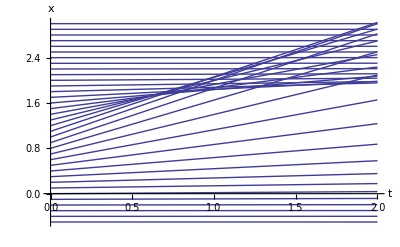

```mathematica
(* Display the characteristics. *)
Plot [ Table[ x[t,x0], {x0, -0.5, 3.0, 0.1}], {t,0.0,2.0}, 
AxesLabel->{Text[Style["t",Italic,23]], Text[Style["x",Italic,23]]}]
```

```mathematica
(* Display the solution u(x,t). *)
ListPlot3D [ {Table[Table[{x[t,x0],t,f[t,x0]}, {x0, -0.5, 3.0, 0.1}], {t,0,2,0.1}]},
ColorFunction->"DarkRainbow",PlotStyle->Directive[Opacity[0.9]],MeshFunctions->{#2 &},
Boxed->False, ImageSize->600, AxesLabel -> {Text[Style["t",Italic,23]], Text[Style["x",Italic,23]],
Text[Style["u",Italic,23]]}]
```